# Metastable states?

### Code and Definitions

Run this code first. Then, you may jump to any subsection.

#### Spin Operators

```mathematica
Id = {{1, 0}, {0, 1}};
Sx= (1/2){{0, 1},{1, 0}};
Sy =(1/2){{0, -I},{I, 0}};
Sz = (1/2){{1, 0},{0, -1}};
```

```mathematica
{MatrixForm[Sx], MatrixForm[Sy], MatrixForm[Sz]}
```

{(0 | 1/2
1/2 | 0),(0 | -ⅈ/2
ⅈ/2 | 0),(1/2 | 0
0 | -1/2)}

#### Local spin exchange Hamiltonian

Isotropic spin-exchange Hamiltonian for adjacent sites on a ring.

```mathematica
h = KroneckerProduct[Sx, Sx]+KroneckerProduct[Sy, Sy]+KroneckerProduct[Sz, Sz] -1/4KroneckerProduct[Id, Id];
```

```mathematica
MatrixForm[h ]
```

(0 | 0 | 0 | 0
0 | -1/2 | 1/2 | 0
0 | 1/2 | -1/2 | 0
0 | 0 | 0 | 0)

#### Probability of finding an up-spin at site x

The following function gives a list of all basis vectors that include an up-spin at site x for a chain of length L. The k-th entry equals 1 if the k-th (configuration) basis vector has an up-spin at state x. Otherwise, the entry is equal to 0. See the next section for an interpretation of the basis vectors as configuration states.

```mathematica
vec[x_, L_]:= Table[If[EvenQ[Floor[k/2^(L-x)]], 1, 0], {k, 0, 2^L-1}]
```

```mathematica
vec[1,5]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

The following function gives the one-point function for the k-th eigenvector. The result is a list of length L so that each entry is {k, p(k)} with k=site and p(k)=probability of measuring an up-spin at site k. 
WARNING: E

```mathematica
Map[Function[x, Abs[x]^2], {1, 2, 3}]
```

{1,4,9}

```mathematica
t[k_,H_]:= Module[{Evec, norm, table, j},
Evec = Eigenvectors[H][[k]]//N;
norm = Norm[Evec]^2;
Evec= Map[Function[x, Abs[x]^2], Evec];
table =Table[{j, N[Dot[Evec, vec[j, L]]/norm]}, {j, 1, L}];
Return[table]
]
```

We rewrite the above function to have the evs=list of eigenvectors as an input so that we don’t have to compute this each time we want to compute the one-point function.

```mathematica
tp[k_, evs_]:= Module[{Evec, norm, table, j},
Evec = evs[[k]]//N;
norm = Norm[Evec]^2;
Evec= Map[Function[x, Abs[x]^2], Evec];
table =Table[{j, N[Dot[Evec, vec[j, M]]/norm]}, {j, 1, L}];
Return[table]
]
```

#### Configurations

We translate between configuration basis and tensor basis, e.g.
{|↑↑⟩,|↑↓⟩, |↓↑⟩, |↓↓⟩} ->{(1
0) ⊗(1
0) , (1
0) ⊗(0
1), (0
1) ⊗(1
0) , (0
1) ⊗(0
1)} ->{(1
0
0
0) , (0
1
0
0)  , (0
0
1
0)   , (0
0
0
1) } 
Let L be the length of the line segment. Denote the basis vectors on the right by e_k, k =1, ..., 2^L, of length/dimension 2^L so that all the entries are zero except for the k-th entry which is 1. The example above is for L=2. We can translate to the configuration basis on the left, i.e. the basis determined by the location of the up-arrows, by writing 2^L-k in base 2. See example below for L=5. The 1-digits represent up-arrows and the 0-digits represent down-arrow. Note that you should think of each number to be made up of L {0,1}-digits by padding 0’s to the left if necessary.

```mathematica
L=5;
Table[BaseForm[2^L-k, 2], {k ,1, 2^L}]
```

{11111_2,11110_2,11101_2,11100_2,11011_2,11010_2,11001_2,11000_2,10111_2,10110_2,10101_2,10100_2,10011_2,10010_2,10001_2,10000_2,1111_2,1110_2,1101_2,1100_2,1011_2,1010_2,1001_2,1000_2,111_2,110_2,101_2,100_2,11_2,10_2,1_2,0_2}

### Hamiltonian for a line segment

#### L=3

Let consider one line segment with L = 3 sites.
    H = Hamiltonian for one line segment of length L.
    hRing = spin exchange operator for the first and last site to make the segment into a ring.
We plot the eigenvalues.

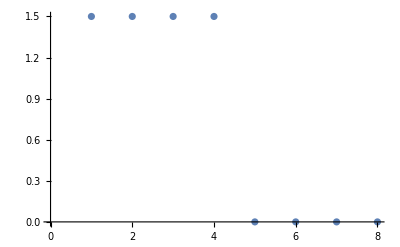

```mathematica
L=3;
hRing = KroneckerProduct[Sx, IdentityMatrix[2^(L-2)], Sx] + KroneckerProduct[Sy, IdentityMatrix[2^(L-2)], Sy]+KroneckerProduct[Sz, IdentityMatrix[2^(L-2)], Sz]-(1/4) IdentityMatrix[2^L];
H = Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], h, IdentityMatrix[2^(L-1-k)]], {k, 1, L-1}] + hRing ;
ListPlot[Eigenvalues[-H]]
```

#### Hamiltonian for the ring of length L and fixed number of down spins

Here we trim the Hamiltonian for the ring only to consider states which contain the specified number of down spins.
For example, with a ring of length L=3, we can consider states which have exactly two down spins

```mathematica
HringNdownspins[L_,NumDownspins_] := Module[{hRing, H,basis,keepIndices,trimmedH}, 
hRing = KroneckerProduct[Sx, IdentityMatrix[2^(L-2)], Sx] + KroneckerProduct[Sy, IdentityMatrix[2^(L-2)], Sy]+KroneckerProduct[Sz, IdentityMatrix[2^(L-2)], Sz]-(1/4) IdentityMatrix[2^L];
H = Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], h, IdentityMatrix[2^(L-1-k)]], {k, 1, L-1}] + hRing ;
basis = Table[IntegerDigits[2^L-k, 2,L], {k ,1, 2^L}];
keepIndices = Flatten[Position[basis,x_/;Count[x,0]==2]];
(*Sanity check if you want to make sure you're keeping the right indices.
for L=3, N=2, indices should be 4, 6, and 7 
Print[keepIndices]; *)
trimmedH = H[[keepIndices,keepIndices]];
Return[trimmedH]
]
H3L2N = HringNdownspins[3,2];
MatrixForm[H3L2N]
```

(-1 | 1/2 | 1/2
1/2 | -1 | 1/2
1/2 | 1/2 | -1)

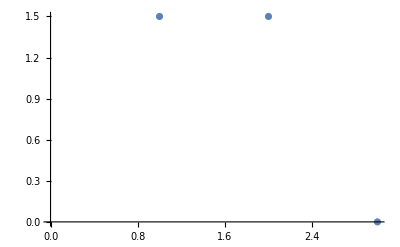

Dot::dotsh: Tensors {1.,0.,1.} and {1,1,1,1,0,0,0,0} have incompatible shapes.

Dot::dotsh: Tensors {1.,0.,1.} and {1.,1.,1.,1.,0.,0.,0.,0.} have incompatible shapes.

Dot::dotsh: Tensors {1.,0.,1.} and {1,1,0,0,1,1,0,0} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

```mathematica
ListPlot[Eigenvalues[-H3L2N]]
Evecs = Eigenvectors[-H3L2N];
Table[t[k, H3L2N], {k, 1, 3}];
```

Table of one-point functions for all eigenstates.

```mathematica
T = Table[t[k], {k, 1, 2^L}];
```

We plot the one-point functions below. We plot states with same eigenvalues together

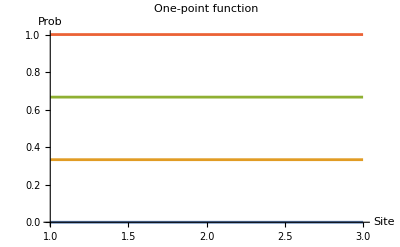

```mathematica
ListPlot[{T[[5]], T[[6]], T[[7]], T[[8]]}, Joined->True, PlotRange->{{1, L}, {0,1}}, PlotLabel-> "One-point function", AxesLabel->{"Site", "Prob"}]
```

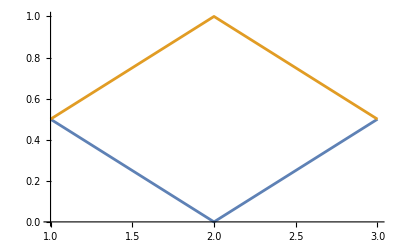

```mathematica
ListPlot[{T[[3]], T[[4]]}, Joined->True, PlotRange->{{1, L}, {0,1}}]
```

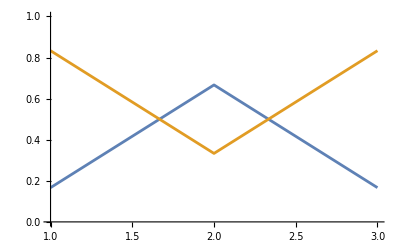

```mathematica
ListPlot[{T[[1]], T[[2]]}, Joined->True, PlotRange->{{1, L}, {0,1}}]
```

#### L= 5

```mathematica
L=5;
```

H  = Hamiltonian

```mathematica
H = Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], h, IdentityMatrix[2^(L-1-k)]], {k, 1, L-1}];
```

Eigenvalues

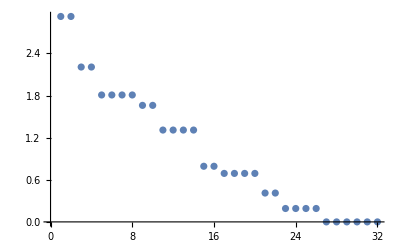

```mathematica
ListPlot[Eigenvalues[-H]]
```

Table of one-point functions

```mathematica
T = Table[t[k], {k, 1, 2^L}];
```

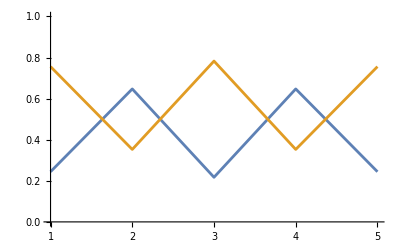

```mathematica
ListPlot[{T[[1]], T[[2]]}, Joined->True, PlotRange->{{1, 5}, {0,1}}]
```

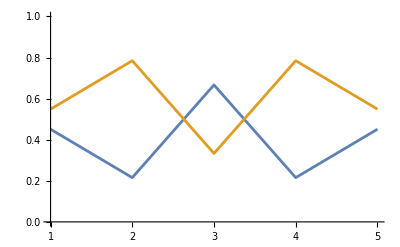

```mathematica
ListPlot[{T[[3]], T[[4]]}, Joined->True, PlotRange->{{1, 5}, {0,1}}]
```

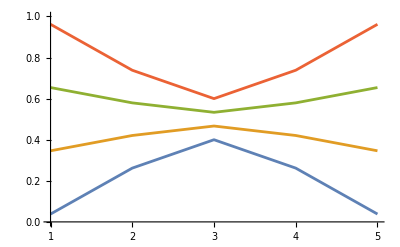

```mathematica
ListPlot[{T[[5]], T[[6]], T[[7]], T[[8]]}, Joined->True, PlotRange->{{1, 5}, {0,1}}]
```

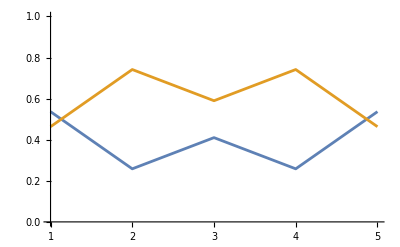

```mathematica
ListPlot[{T[[9]], T[[10]]}, Joined->True, PlotRange->{{1, 5}, {0,1}}]
```

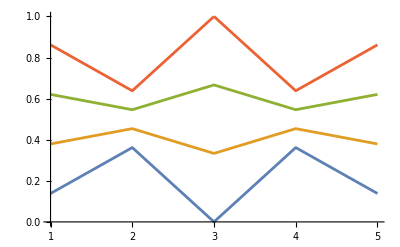

```mathematica
ListPlot[{T[[11]], T[[12]], T[[13]], T[[14]]}, Joined->True, PlotRange->{{1, 5}, {0,1}}]
```

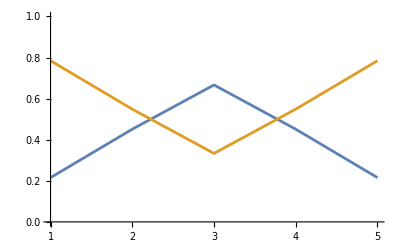

```mathematica
ListPlot[{T[[15]], T[[16]]}, Joined->True, PlotRange->{{1, 5}, {0,1}}]
```

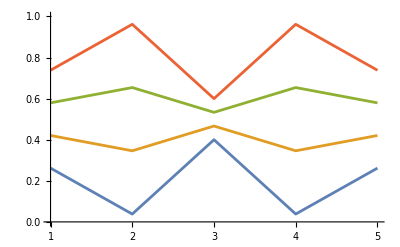

```mathematica
ListPlot[{T[[17]], T[[18]], T[[19]], T[[20]]}, Joined->True, PlotRange->{{1, 5}, {0,1}}]
```

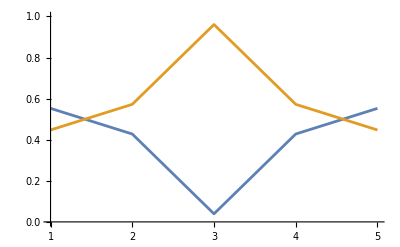

```mathematica
ListPlot[{T[[21]], T[[22]]}, Joined->True, PlotRange->{{1, 5}, {0,1}}]
```

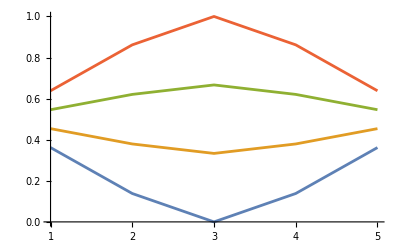

```mathematica
ListPlot[{T[[23]], T[[24]], T[[25]], T[[26]]}, Joined->True, PlotRange->{{1, 5}, {0,1}}]
```

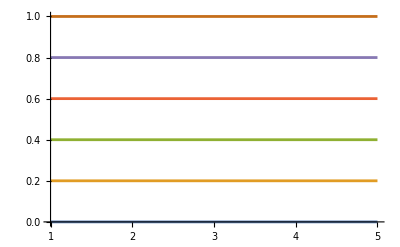

```mathematica
ListPlot[{T[[27]], T[[28]], T[[29]], T[[30]], T[[31]], T[[32]]}, Joined->True, PlotRange->{{1, 5}, {0,1}}]
```

### Parallel lines

Let’s do two parallel lines. 
    M= total number of sites. 
    L= sites per layer = M/2.
    H1 = Hamiltonian for first layer.
    H2 = Hamiltonian for second layer.
    H12 = Hamiltonian between layers.
    Hp = Hamiltonian for parallel layers.

#### L=3

```mathematica
M=6;
L=3;
```

```mathematica
H1 = Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], h, IdentityMatrix[2^(M-k-1)]], {k, 1, L-1}] ;
```

```mathematica
H2 = Sum[KroneckerProduct[IdentityMatrix[2^(L +k-1)], h, IdentityMatrix[2^(L-k-1)]], {k, 1, L-1}] ;
```

```mathematica
H12 = Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], Sx, IdentityMatrix[2^(L-1)], Sx, IdentityMatrix[2^(L-k)]], {k, 1, L}]+Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], Sy, IdentityMatrix[2^(L-1)], Sy, IdentityMatrix[2^(L-k)]], {k, 1, L}]+ Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], Sz, IdentityMatrix[2^(L-1)], Sz, IdentityMatrix[2^(L-k)]], {k, 1, L}] - (L/4)IdentityMatrix[2^M];
```

```mathematica
Hp = -H1 - H2 + (1/10)H12;
```

Eigenvalues

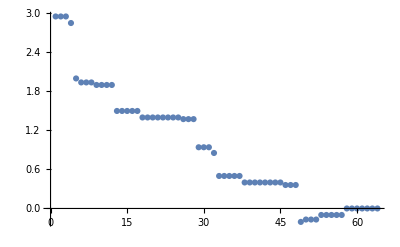

```mathematica
ListPlot[Eigenvalues[Hp]]
```

Eigenvectors

```mathematica
EVs =Eigenvectors[Hp];
```

Table of one-point functions

```mathematica
Tp = Table[tp[k, EVs], {k, 1, 2^M}];
```

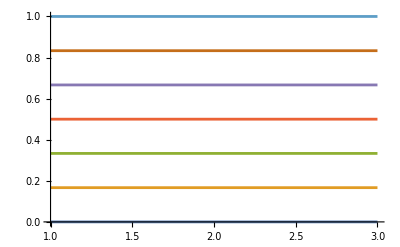

```mathematica
ListPlot[{Tp[[58]], Tp[[59]], Tp[[60]],Tp[[61]], Tp[[62]], Tp[[63]], Tp[[64]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

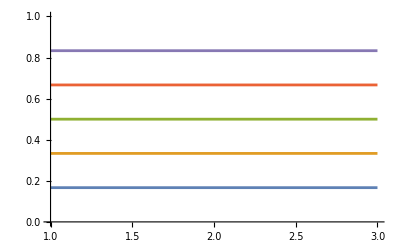

```mathematica
ListPlot[{Tp[[53]], Tp[[54]], Tp[[55]],Tp[[56]], Tp[[57]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

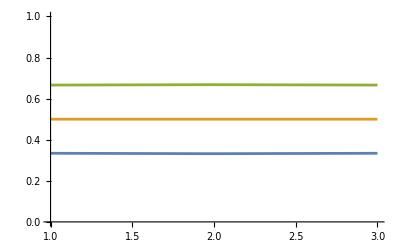

```mathematica
ListPlot[{Tp[[50]], Tp[[51]], Tp[[52]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

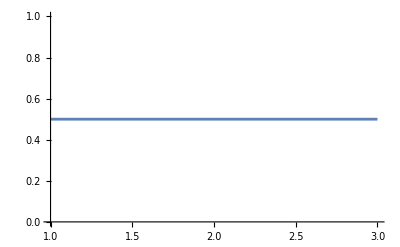

```mathematica
ListPlot[{Tp[[49]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

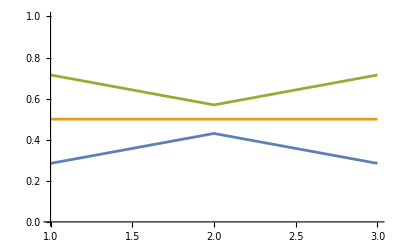

```mathematica
ListPlot[{Tp[[46]], Tp[[47]], Tp[[48]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

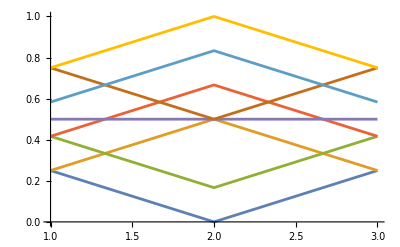

```mathematica
ListPlot[{Tp[[38]], Tp[[39]], Tp[[40]],Tp[[41]], Tp[[42]], Tp[[43]], Tp[[44]], Tp[[45]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

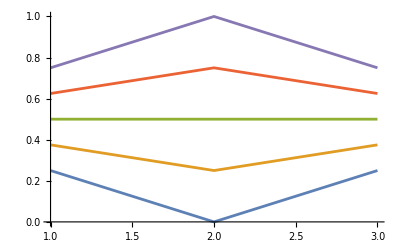

```mathematica
ListPlot[{Tp[[33]], Tp[[34]], Tp[[35]],Tp[[36]], Tp[[37]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

```mathematica
ListPlot[{Tp[[32]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

-Graphics-

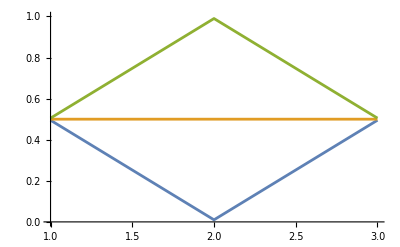

```mathematica
ListPlot[{Tp[[29]], Tp[[30]], Tp[[31]]}, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

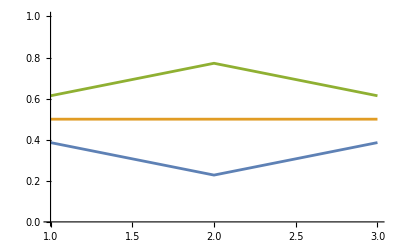

```mathematica
ListPlot[{Tp[[26]], Tp[[27]], Tp[[28]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

### L=4

Let’s do two parallel lines

```mathematica
M=8;
L=4;
```

```mathematica
H1 = Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], h, IdentityMatrix[2^(M-k-1)]], {k, 1, L-1}] ;
```

```mathematica
H2 = Sum[KroneckerProduct[IdentityMatrix[2^(L +k-1)], h, IdentityMatrix[2^(L-k-1)]], {k, 1, L-1}] ;
H12 = Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], Sx, IdentityMatrix[2^(L-1)], Sx, IdentityMatrix[2^(L-k)]], {k, 1, L}]+Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], Sy, IdentityMatrix[2^(L-1)], Sy, IdentityMatrix[2^(L-k)]], {k, 1, L}]+ Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], Sz, IdentityMatrix[2^(L-1)], Sz, IdentityMatrix[2^(L-k)]], {k, 1, L}] - (L/4)IdentityMatrix[2^M];
```

```mathematica
Hp = -H1 - H2 + (1/10)H12;
```

Eigenvalues

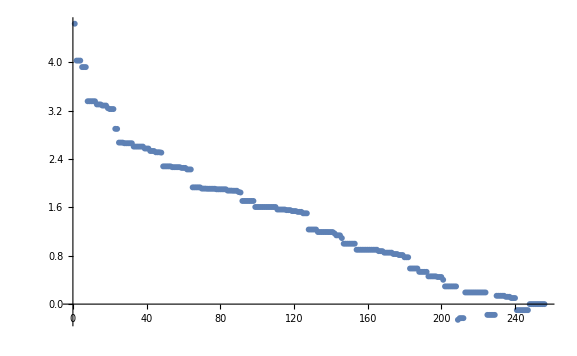

```mathematica
ListPlot[Eigenvalues[Hp]]
```

Eigenvectors

```mathematica
EVs =Eigenvectors[Hp];
```

Table of one-point functions.
WARNING: The code seems to break down. Not sure why. It seems like we are dividing by zero.

```mathematica
Tp = Table[tp[k, EVs], {k, 1, 2^M}];
```

General::munfl: 1.14204×10^-79 2.18165×10^-288 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.77277×10^-225 8.23469×10^-192 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 6.39508×10^-214 4.67109×10^-110 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Power::infy: Infinite expression 1/0.^1. encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity ComplexInfinity ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
Tp[[209]]
```

{{1,0.5},{2,0.5},{3,0.5},{4,0.5}}

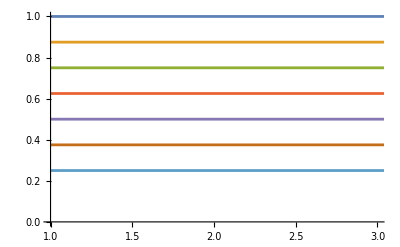

```mathematica
ListPlot[{Tp[[256]], Tp[[255]], Tp[[254]],Tp[[253]], Tp[[252]], Tp[[251]], Tp[[250]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

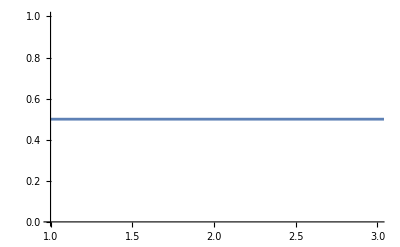

```mathematica
ListPlot[{Tp[[209]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

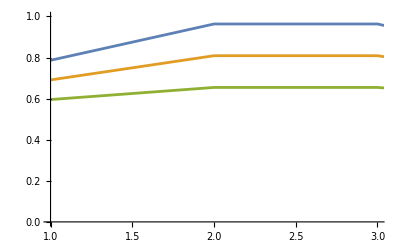

```mathematica
ListPlot[{Tp[[208]], Tp[[207]], Tp[[206]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

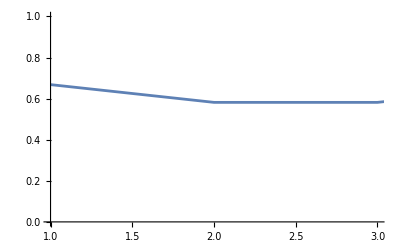

```mathematica
ListPlot[{Tp[[237]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

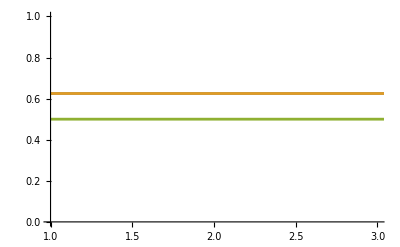

```mathematica
ListPlot[{Tp[[162]], Tp[[161]], Tp[[160]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

```mathematica
ListPlot[{Tp[[38]], Tp[[39]], Tp[[40]],Tp[[41]], Tp[[42]], Tp[[43]], Tp[[44]], Tp[[45]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

-Graphics-

```mathematica
ListPlot[{Tp[[33]], Tp[[34]], Tp[[35]],Tp[[36]], Tp[[37]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

-Graphics-

```mathematica
ListPlot[{Tp[[100]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

-Graphics-

```mathematica
ListPlot[{Tp[[29]], Tp[[30]], Tp[[31]]}, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

-Graphics-

```mathematica
ListPlot[{Tp[[26]], Tp[[27]], Tp[[28]] }, Joined->True, PlotRange->{{1, 3}, {0,1}}]
```

-Graphics-